```mathematica
(*This is the path that contains the executables and loads SDPB*)
executablesPath = "/home/pano/.local/src/sdpb/build";
<<"/home/pano/.local/src/sdpb/mathematica/SDPB.m";
```

# Gap Consistency Checks

## We constrain possible values for the Gap of a CFT by searching for a functional which breaks everything hehe.

## Defining the Matrix Problem

Let’s first construct the matrix problem and tell SDPB to export the description into a JSON file for SDPB to actually run the thing.

terminateReason = "found primal-dual optimal solution";
primalObjective = -0.08412277664469908199714525625509274180504614741651893059464274110963781201827453226366549811612964837890531014174961956695379460016835742978661833137092431607748751427659607620736281994291067811388398960222818264153858618364078592850869944010862648932233827635114616876921900002246188171676701590386028152242589;
dualObjective   = -0.08412277664469908199714525625565306568354903420585865453847243744468498589806779161357147528252069825065763970900089487365606723020134376345882409281579907366492244323629166419313830450457890806613996630847536263233520505328789525870478987599545691947328312051063719853115796645291012332725031159375360539173292;
dualityGap      = 5.603238785028867893397239438296963350471738797932593499059771663910498717523295672512753067022726300329863336722057614448747575874349289596955879857754845616682299522559767062471799907966188696471093301960904358868304301509448441594910297619389664304482416104832956898933238693070275258506426272125200703804886e-31;
primalError     = 1.356075592855448539600479696651513695156743570910495711501423553877597031655014760793434322613005334270095174163960682267599746651796657086555891543422256953833167789341277120893501711710732437173907642414125135096941250373700132322974812443681654176106216131710584140637266087067139872128078593495635293961478e-251;
dualError       = 4.30385186016545074016657313113865897199575921632293458415133491271811587588499390859819164517073222466669813359901109367702469547785921837612950331364212950033773934112567620943732863345963032735391951404382914647052057558230187209451460819012838440123896703214586284817046437948801590039748133460880081106041e-267;
Solver runtime  = 12;

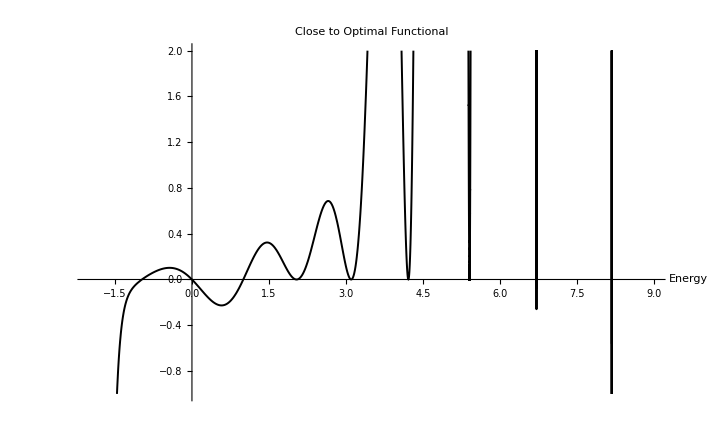

```mathematica
(*Precision and directories*)
precision = 1024;
file ="/home/pano/projects/sdpb-test/pmp.json";
sdpdir="/home/pano/projects/sdpb-test/sdp";
outdir="/home/pano/projects/sdpb-test/out";
outfile ="/home/pano/projects/sdpb-test/out/z.txt";
Run[StringRiffle[{
"rm -rf",
FileNameJoin[{sdpdir,"*"}],
sdpdir<>".ck",
FileNameJoin[{outdir,"*"}]
}]];

(*Maximum order of derivatives in the linear functional a*)
P=35; 

(*Central charge*)
c = 12; 

(*Threshold*)
threshold=1; 

(*Gap energy*)
E0=1+ 0.001; 

(*Polynomial generator function*)
poly[n_,E0_,x_]:=Sum[StirlingS2[n,k](-2π (x+E0))^k,{k,1,n}]; 

(*Construct a module that does this whole sdpb definition thingy*)
solve[gapEnergy_:E0,centralCharge_:c, order_:P, precision_:precision,thresh_:threshold]:=
Module[{
E0=gapEnergy,
c=centralCharge,
NN=Floor[order/2],
threshold=thresh,
objective,
normalization,
matrices
},

(*Objective vector*)
(*objective = {0}~Join~(poly[2#+1,0,-c/12]&/@Range[0,NN]);*)
objective = (poly[2#+1,0,-c/12]&/@Range[0,NN]);
(*objective = {0}~Join~(-(poly[2#+1,0,-c/12]&/@Range[0,NN]));*)

(*Normalization vector*)
(*normalization = {1}~Join~(Range[0,NN]*0);*)
normalization = (poly[2#+1,0,-c/(12*2)]&/@Range[0,NN])*threshold;
(*normalization = {1}~Join~(Range[0,NN]*0);*)

(*Polynomial list*)
matrices={
PositiveMatrixWithPrefactor[<|
(*"polynomials"->{{{0}~Join~(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}*)
"polynomials"->{{(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}
(*"polynomials"->{{{0}~Join~(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}*)
|>]
(*,PositiveMatrixWithPrefactor[<|
"prefactor"-> 1,
"polynomials"->{{{-threshold}~Join~(poly[2#+1,0,-c/12]&/@Range[0,NN])}}
|>]*)
};

(*Define SDP*)
WritePmpJson[file, SDP[objective,normalization,matrices], precision];

(*Run the magical code to solve*)
Run[StringRiffle[{
FileNameJoin[{executablesPath,"pmp2sdp"}],
ToString[precision], file, sdpdir
}]];
Run[StringRiffle[{
"mpirun"
,FileNameJoin[{executablesPath,"sdpb"}]
,"-s", sdpdir, "-o", outdir
,"--precision="<> ToString[precision]
,"--noFinalCheckpoint"
,"--maxIterations="<>ToString[5000]
,"--dualityGapThreshold=1e-30"
, "--writeSolution=\"x,y,z\""
,"--maxComplementarity=1e+400"
(*,"--findDualFeasible"*)
}]];
(*ToExpression@Import[FileNameJoin[{outdir,"out.txt"}],"Text"];*)
fullResult = Import[FileNameJoin[{outdir,"out.txt"}], "String"];
Echo[fullResult];
];
solve[]
(* Get the optimal vector *)
α=(Import[outfile,"Table"][[2;;]]//Flatten).(poly[2#+1,0,x]&/@Range[0,Floor[P/2]])//Simplify;
Plot[α/threshold/10,{x,-c/12-E0,9},PlotRange->{-1,2} ,MaxRecursion->15,AxesLabel->{HoldForm[Energy],None},PlotLabel->HoldForm[Close to Optimal Functional],LabelStyle->{8},PlotStyle->{Black,Thickness[0.002]}]
```

{-0.0841228,0.,-0.00961503,0.0457471,1.17454}

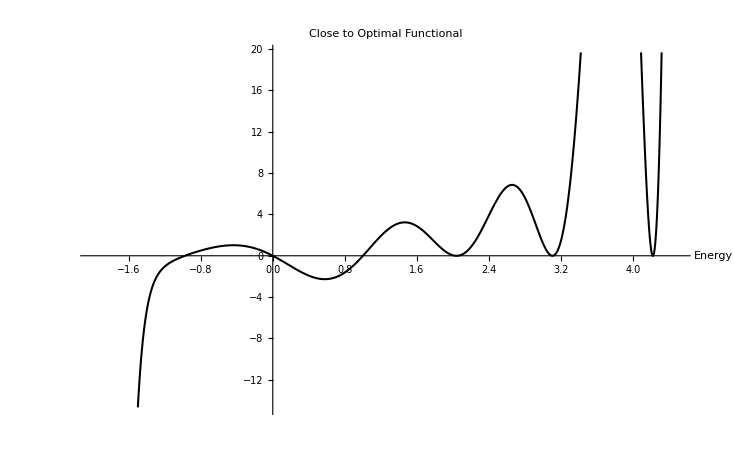

```mathematica
α=(Import[outfile,"Table"][[2;;]]//Flatten).(poly[2#+1,0,x]&/@Range[0,Floor[P/2]])//Simplify;
Echo[N[(α/threshold)/.x->(#)]& /@{-1,0,1,2,3}];
Plot[α/threshold,{x,-c/12-E0,4.5},MaxRecursion->15,AxesLabel->{HoldForm[Energy],None},PlotLabel->HoldForm[Close to Optimal Functional],LabelStyle->{8},PlotStyle->{Black,Thickness[0.002]}]
```

```mathematica
(α/.x->(-1))
```

0.19943084485531250175623889472225721513387088454163240655507171148724888018678934380617477559586336564042131310147044319087330814515137410478451079461343757447956408354641122720321285217749193099816139581096686569870775555579921505758215811092309354092240565287532623622431120788454731901758997289571953

```mathematica
StringRiffle[{
"rm -rf",
FileNameJoin[{sdpdir,"*"}],
sdpdir<>".ck",
FileNameJoin[{outdir,"*"}],
"&&",
FileNameJoin[{executablesPath,"pmp2sdp"}],
ToString[precision], file, sdpdir,
 "&&",
"mpirun",
FileNameJoin[{executablesPath,"sdpb"}],
"-s", sdpdir, "-o", outdir,
"--precision="<> ToString[precision],
"--noFinalCheckpoint"
,"--maxIterations="<>ToString[5000]
,"--dualityGapThreshold=1e-10"
, "--writeSolution=\"x,y,z\""
}]//CopyToClipboard
```

```mathematica
poly[7,0,x/(-2Pi)]
```

x+63 x^2+301 x^3+350 x^4+140 x^5+21 x^6+x^7

```mathematica
(α)/threshold//N//Expand
```

-4.13381 x-3.12634 x^2+4.59261 x^3+4.98869 x^4-0.142916 x^5-2.2316 x^6-0.893764 x^7+0.233551 x^8+0.30482 x^9+0.0615127 x^10-0.0256393 x^11-0.0210809 x^12-0.00104234 x^13+0.000219417 x^14+0.00180043 x^15-0.000876047 x^16+0.000757069 x^17-0.000667915 x^18+0.000483209 x^19-0.000322861 x^20+0.000191185 x^21-0.0000978238 x^22+0.0000430963 x^23-0.0000161638 x^24+5.09647×10^-6 x^25-1.33553×10^-6 x^26+2.86667×10^-7 x^27-4.94657×10^-8 x^28+6.7179×10^-9 x^29-7.01648×10^-10 x^30+5.48271×10^-11 x^31-3.08606×10^-12 x^32+1.17808×10^-13 x^33-2.72441×10^-15 x^34+2.87697×10^-17 x^35